{{0.0923341,0.0134234},{0.297486,0.294947},{0.429349,0.451717},{0.915188,0.815108},{1.07081,0.806356},{1.79854,0.927812},{3.43202,-0.292294},{4.35861,-0.937147},{4.46764,-0.895071},{5.84828,-0.310382}}

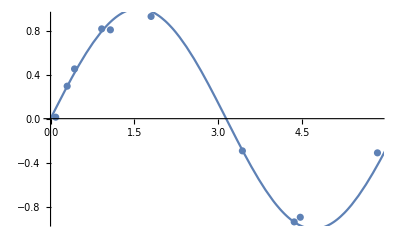

```mathematica
biasMeta=0.07;
nMeta=10;
xi=Sort@RandomReal[{0,2 Pi},nMeta];

TrainingSet=Table[{xi[[n]],Sin[xi[[n]]]+RandomVariate[NormalDistribution[0,biasMeta]]},{n,1,nMeta}]
Show[ListPlot[TrainingSet],Plot[Sin[x],{x,0,2Pi}]]
```

0.568778-0.139834 x-0.0181077 x^2

Inverse::luc: 病态矩阵 {{10.,22.7103,90.4387,420.344,2080.36,10691.3},{22.7103,90.4387,420.344,2080.36,10691.3,56488.3},{90.4387,«19»,«18»,«19»,«18»,305071.},«1»,{2080.36,10691.3,56488.3,305071.,1.67677×10^6,9.34607×10^6},{10691.3,56488.3,305071.,1.67677×10^6,9.34607×10^6,5.26733×10^7}} 构成的 Inverse 的结果可能包含明显的数值错误.

Inverse::luc: 病态矩阵 {{10.,22.7103,90.4387,420.344,2080.36,10691.3,56488.3,305071.,1.67677×10^6,9.34607×10^6},«8»,{9.34607×10^6,5.26733×10^7,2.99439×10^8,1.71371×10^9,9.85848×10^9,5.69377×10^10,3.29839×10^11,1.91514×10^12,1.11393×10^13,6.48774×10^13}} 构成的 Inverse 的结果可能包含明显的数值错误.

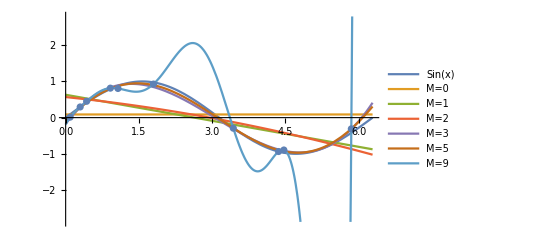

```mathematica
h[T_,M_]:=Module[{},
sumx=Table[∑_(i=1)^nMeta T[[i,1]]^j,{j,0,2M}];
sumxy=Table[{∑_(i=1)^nMeta T[[i,1]]^j T[[i,2]]},{j,0,M}];
sx=Table[sumx[[x+y-1]],{x,1,M+1},{y,1,M+1}];
wj=Inverse[sx]. sumxy;
Sum[wj[[j,1]] x^(j-1),{j,1,M+1}]
]
h[TrainingSet,2]
Show[Plot[{Sin[x],h[TrainingSet,0],h[TrainingSet,1],h[TrainingSet,2],h[TrainingSet,3],h[TrainingSet,5],h[TrainingSet,9]},{x,0,2Pi},PlotLegends->{"Sin(x)","M=0","M=1","M=2","M=3","M=5","M=9"}],ListPlot[TrainingSet]]
(*ListPlot[{fm[T,nMeta,3],T}]*)
```